```mathematica
(*InverseFourierTransform[Cos[k],k,x]*)
```

```mathematica
Func[x_]:=Cos[x^3]
```

```mathematica
FT[k_]:=FourierTransform[Func[x],x,k]
```

```mathematica
FT[k]
```

1/2 (Cos[k^2/4]+Sin[k^2/4])

```mathematica
√(π/2) DiracDelta[-2+k]+√(π/2) DiracDelta[2+k]
```

√(π/2) DiracDelta[-2+k]+√(π/2) DiracDelta[2+k]

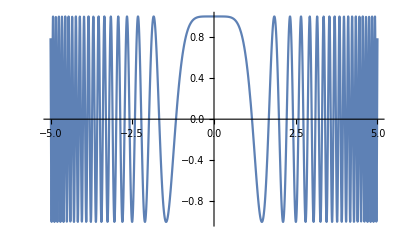

```mathematica
Plot[Func[x],{x,-5,5}]
```

```mathematica
R=0.5;
```

```mathematica
64^3
```

262144

```mathematica
Func2=InverseFourierTransform[(FT[k])E^(-k^2 R^2/2),k,x]//FullSimplify
```

(0.460221-0.108643 ⅈ) ⅇ^((-0.4-0.8 ⅈ) x^2)+(0.460221+0.108643 ⅈ) ⅇ^((-0.4+0.8 ⅈ) x^2)

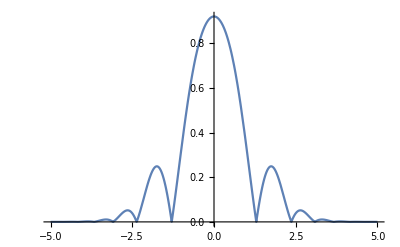

```mathematica
Plot[Abs[Func2],{x,-5,5},PlotRange->Full]
```